```mathematica
SetDirectory[NotebookDirectory[]];
{ti, tf, dt}={0.001,2 π*10+ti, dt=(tf-ti)/3};
{αi,αf,dα} = {π/4,π/4,1};
{βi,βf,dβ}={π/4,π/4,1};

a0=1.;
(* q=10^-19;
h=1.054571800 10^-34;
c=3 10^8; *)
me=ϵ0=1;
q=h=c=1;
e=1;
a10=1.;
a20=1.;
ωf1=1.;
ωf2=0.5;
t0=30.;
τ=20.;
neq=3;
nmax=3;
m[m1_, m2_]:=m1-m2;
int[n1_, l1_, n2_, l2_ , l_, t_]:=int[n1, l1, n2, l2, l, t];
R[n_, l_,r_]:=1/(√(2 n (n-l-1)! (n+l)!)) (2/(n a0))^(3/2) ⅇ^(-r/(n a0))((2 r)/(n a0))^l LaguerreL[n-l-1,2 l+1, (2 r)/(n a0)];
Y[l_, m_, θ_, ϕ_]:=I^l SphericalHarmonicY[l, m,θ, ϕ];
a1[t_]:=a10 Exp[-(t-t0)^2/τ^2] Sin[t ωf1];
a2[t_]:=a20 Exp[-(t-t0)^2/τ^2] Sin[t ωf2];
asum[t_]:=√((a1[t])^2+(a2[t])^2);


θ1[α_, β_, t_] := ArcCos[a2[t] Cos[α]/asum[t]];
ϕ1[α_, β_, t_]:= ArcTan[(a1[t] Sin[α]-a2[t] Cos[α] Sin[β])/(a1[t] Cos[α]+a2[t] Sin[α] Sin[β] )];



int[2, 1, 2, 1, 0, t_]:=-((c^6 h^6 q (-c h+a0 asum[t] q) (c h+a0 asum[t] q))/(c^2 h^2+a0^2 (asum[t])^2 q^2)^4);
int[2, 1, 2, 1,1, t_]:=-((a0 asum[t] c^5 h^5 (a0^2 (asum[t])^2-5 c^2 h^2))/(3 (a0^2 (asum[t])^2+c^2 h^2)^4));
int[2, 1, 2, 1,2, t_]:=(2 a0^2 (asum[t])^2 c^6 h^6)/((a0^2 (asum[t])^2+c^2 h^2)^4);
int[3, 0, 2, 1, 1,t_]:=Piecewise[{{(72 √2 c h (asum[t] q Cos[(asum[t] q)/(c h)]-c h Sin[(asum[t] q)/(c h)]))/(3125 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 0, 1,t_]:=Piecewise[{{(72 √2 c h (asum[t] q Cos[(asum[t] q)/(c h)]-c h Sin[(asum[t] q)/(c h)]))/(3125 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[3, 2, 2, 1, 1,t_]:=Piecewise[{{(4608 c h (-asum[t] q Cos[(asum[t] q)/(c h)]+c h Sin[(asum[t] q)/(c h)]))/(3125 √5 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 2, 1,t_]:=Piecewise[{{(4608 c h (-asum[t] q Cos[(asum[t] q)/(c h)]+c h Sin[(asum[t] q)/(c h)]))/(3125 √5 (asum[t])^2 q^2),asum[t]≠0},{0,asum[t]=0}}];
int[3, 2, 2, 1, 2,t_]:=Piecewise[{{-((4608 c h (3 asum[t] c h q Cos[(asum[t] q)/(c h)]+(-3 c^2 h^2+asum[t]^2 q^2) Sin[(asum[t] q)/(c h)]))/(3125 √5 asum[t]^3 q^3)),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 2, 2,t_]:=Piecewise[{{-((4608 c h (3 asum[t] c h q Cos[(asum[t] q)/(c h)]+(-3 c^2 h^2+asum[t]^2 q^2) Sin[(asum[t] q)/(c h)]))/(3125 √5 asum[t]^3 q^3)),asum[t]≠0},{0,asum[t]=0}}];
int[3, 2, 2, 1, 3,t_]:=Piecewise[{{1/(3125 √5 (asum[t])^4 q^4)4608 c h (asum[t] q (-15 c^2 h^2+(asum[t])^2 q^2) Cos[(asum[t] q)/(c h)]+3 c h (5 c^2 h^2-2 (asum[t])^2 q^2) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];
int[2, 1, 3, 2, 3,t_]:=Piecewise[{{1/(3125 √5 (asum[t])^4 q^4)4608 c h (asum[t] q (-15 c^2 h^2+(asum[t])^2 q^2) Cos[(asum[t] q)/(c h)]+3 c h (5 c^2 h^2-2 (asum[t])^2 q^2) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];
int[2,1,3,1,0,t_]:=(331776 (125 a0^2 asum[t]^2 c^8 h^8 q^2-108 a0^4 asum[t]^4 c^6 h^6 q^4))/(25 c^2 h^2+36 a0^2 asum[t]^2 q^2)^5
int[3,1,2,1,0,t_]:=(331776 (125 a0^2 asum[t]^2 c^8 h^8 q^2-108 a0^4 asum[t]^4 c^6 h^6 q^4))/(25 c^2 h^2+36 a0^2 asum[t]^2 q^2)^5;
int[2,1,3,1,2,t_]:=(663552 a0^2 c^6 h^6 q^2 asum[t]^2 (-25 c^2 h^2+108 a0^2 q^2 asum[t]^2))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5;
int[3,1,2,1,2,t_]:=(663552 a0^2 c^6 h^6 q^2 asum[t]^2 (-25 c^2 h^2+108 a0^2 q^2 asum[t]^2))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5;
int[2,1,3,1,1,t_]:=-((9216 a0 c^5 h^5 q asum[t] (625 c^4 h^4-6840 a0^2 c^2 h^2 q^2 asum[t]^2+1296 a0^4 q^4 asum[t]^4))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5);
int[3,1,2,1,1,t_]:=-((9216 a0 c^5 h^5 q asum[t] (625 c^4 h^4-6840 a0^2 c^2 h^2 q^2 asum[t]^2+1296 a0^4 q^4 asum[t]^4))/(25 c^2 h^2+36 a0^2 q^2 asum[t]^2)^5);

int[3,1,3,1,1,t_]:=-((128 a0 asum[t] c^5 h^5 q (-400 c^6 h^6+3672 a0^2 asum[t]^2 c^4 h^4 q^2-8505 a0^4 asum[t]^4 c^2 h^2 q^4+1458 a0^6 asum[t]^6 q^6))/(3 (4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6));
int[3,1,3,1,2,t_]:=(1536 a0^2 c^6 h^6 q^2 asum[t]^2 (32 c^4 h^4-180 a0^2 c^2 h^2 q^2 asum[t]^2+243 a0^4 q^4 asum[t]^4))/(4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6;
int[3,1,3,2,1,t_]:=-((384 √5 a0 asum[t] c^7 h^7 q (16 c^4 h^4-120 a0^2 asum[t]^2 c^2 h^2 q^2+81 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,2,3,1,1,t_]:=-((384 √5 a0 asum[t] c^7 h^7 q (16 c^4 h^4-120 a0^2 asum[t]^2 c^2 h^2 q^2+81 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,1,3,2,2,t_]:=-((768 a0^2 c^6 h^6 q^2 asum[t]^2 (112 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+81 a0^4 q^4 asum[t]^4))/(√5 (4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6));
int[3,2,3,1,2,t_]:=-((768 a0^2 c^6 h^6 q^2 asum[t]^2 (112 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+81 a0^4 q^4 asum[t]^4))/(√5 (4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6));
int[3,2,3,1,3,t_]:=Piecewise[{{-1/(3 asum[t]^4 q^4)√5 c h (asum[t] q (-15 c^2 h^2+asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(15 c^3 h^3-asum[t]^3 q^3) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];
int[3,1,3,2,3,t_]:=Piecewise[{{-1/(3 asum[t]^4 q^4)√5 c h (asum[t] q (-15 c^2 h^2+asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(15 c^3 h^3-asum[t]^3 q^3) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];

int[3,2,3,0,2,t_]:=(384 √(2/5) a0^2 c^6 h^6 q^2 asum[t]^2 (80 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+243 a0^4 q^4 asum[t]^4))/(4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6;
int[3,0,3,2,2,t_]:=(384 √(2/5) a0^2 c^6 h^6 q^2 asum[t]^2 (80 c^4 h^4-432 a0^2 c^2 h^2 q^2 asum[t]^2+243 a0^4 q^4 asum[t]^4))/(4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6;

int[3,1,3,1,0,t_]:=(256 c^6 h^6 (c h-3 a0 asum[t] q) (c h+3 a0 asum[t] q) (4 c^2 h^2-27 a0^2 asum[t]^2 q^2) (4 c^2 h^2-3 a0^2 asum[t]^2 q^2))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6;

int[3,2,3,2,3,t_]:=Piecewise[{{1/(asum[t]^4 q^4)c h (asum[t] q (-15 c^2 h^2+asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(15 c^3 h^3-asum[t]^3 q^3) Sin[(asum[t] q)/(c h)]),asum[t]≠0},{0,asum[t]=0}}];

int[3,2,3,2,0,t_]:=(256 c^8 h^8 (16 c^4 h^4-120 a0^2 asum[t]^2 c^2 h^2 q^2+81 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6;
int[3,2,3,2,1,t_]:=(128 a0 asum[t] c^7 h^7 q (560 c^4 h^4-1512 a0^2 asum[t]^2 c^2 h^2 q^2+243 a0^4 asum[t]^4 q^4))/(5 (4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,2,3,2,2,t_]:=(6144 a0^2 asum[t]^2 c^8 h^8 q^2 (28 c^2 h^2-27 a0^2 asum[t]^2 q^2))/(5 (4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6);
int[3,2,3,2,4,t_]:=1/(asum[t]^5 q^5)c h (5 asum[t] c h q (-21 c^2 h^2+2 asum[t]^2 q^2) Cos[(asum[t] q)/(c h)]+(105 c^4 h^4-45 asum[t]^2 c^2 h^2 q^2+asum[t]^4 q^4) Sin[(asum[t] q)/(c h)]);
int[3,0,3,1,1,t_]:=1/((4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6)48 √2 a0 c^5 h^5 q asum[t] (-128 c^6 h^6+1392 a0^2 c^4 h^4 q^2 asum[t]^2-3888 a0^4 c^2 h^2 q^4 asum[t]^4+2187 a0^6 q^6 asum[t]^6);
int[3,1,3,0,1,t_]:=1/((4 c^2 h^2+9 a0^2 q^2 asum[t]^2)^6)48 √2 a0 c^5 h^5 q asum[t] (-128 c^6 h^6+1392 a0^2 c^4 h^4 q^2 asum[t]^2-3888 a0^4 c^2 h^2 q^4 asum[t]^4+2187 a0^6 q^6 asum[t]^6);
int[3,0,3,0,0,t_]:=(4 c^4 h^4 (4 c^2 h^2-27 a0^2 asum[t]^2 q^2) (4 c^2 h^2-3 a0^2 asum[t]^2 q^2) (16 c^4 h^4-216 a0^2 asum[t]^2 c^2 h^2 q^2+243 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6

vv[n1_, l1_, m1_, n2_, l2_, m2_, t_,  α_, β_]:=  ∑_(l=Abs[l1-l2])^(l1+l2) Y[l, m[m1, m2],θ1[α, β, t], ϕ1[α, β, t]]  (-1)^m1 I^(l1-l2)ThreeJSymbol[{l1,-m1},{l,m[m1, m2]},{l2,m2}] ThreeJSymbol[{l1,0},{l,0},{l2,0}] √(4 π(2l1+1)(2l+1)(2l2+1))int[n1, l1, n2, l2, l, t];

v[n1_, l1_, m1_, n2_, l2_, m2_, t_,α_, β_]:=Conjugate[vv[n2, l2, m2, n1, l1, m1, t, α, β]];
ω[n1_, n2_]:=-(me e^4)/(8 h^2 ϵ0^2)(1/n1^2-1/n2^2);

ee[n4_]:= Abs[- (me e^4)/(8 h^2 ϵ0^2) 1/n4^2]; (* энергия *)


r[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=∑_(n3=2)^nmax ∑_(l3=1)^(n3-1) ∑_(m3=-l3)^l3 vv[n1, l1, m1, n3, l3, m3, t, α, β]ee[n3]  v[n3, l3, m3, n2, l2, m2, t,α, β]+vv[n1, l1, m1, 3, 0, 0, t, α, β]ee[3]  v[3, 0,0, n2, l2, m2, t,α, β]+vv[3,0,0,n2,l2,m2, t, α, β]ee[3]  v[n1,l1,m1,3,0,0, t,α, β];
```

```mathematica
(* почему есть neq и nmax? чем они отличаются? *)
Print["t_elem = ",Length[Table[t, {t,ti,tf,dt}]], ", t = ", {ti,tf,dt}];
Print["α_elem = ",Length[Table[α, {α,αi,αf,dα}]], ", α = ", {αi,αf,dα}];
Print["β_elem = ",Length[Table[β, {β,βi,βf,dβ}]], ", β = ", {βi,βf,dβ}];
```

t_elem = 4, t = {0.001,62.8329,20.944}

α_elem = 1, α = {π/4,π/4,1}

β_elem = 1, β = {π/4,π/4,1}

```mathematica
LocalTime[]
Print["t=",Dynamic[t], ", α=",Dynamic[α], ", β=",Dynamic[β],", n1=",Dynamic[n1], ", l1=",Dynamic[l1], ", m1=",Dynamic[m1], ", n2=",Dynamic[n2], ", l2=",Dynamic[l2], ", m2=",Dynamic[m2]];
(* можно и так пробовать, вывод идет в отдельное окно *)
(* Dynamic[Print["t=",t," α=",α, " β=",β," n1=",n1, " l1=",l1, " m1=",m1, " n2=",n2, " l2=",l2, " m2=",m2];]; *)

(* мы по сути ничего не теряем, если считаем для vv, только выйгрыш в 6 раз против r *)
Monitor[vvtable=Table[
If[2<=n1<=neq && 1<=l1<=n1-1 && -l1<=m1<=l1&&2<=n2<=nmax&&1<=l2<=n2-1&& -l2<=m2<=l2,vv[n1, l1, m1, n2, l2, m2, t ,α, β], 
0],
{t,ti,tf,dt} ,{α,αi,αf,dα}, {β,βi,βf,dβ},{n1, 2, neq},{l1, 1, neq-1}, {m1, -neq, neq}, {n2, 2, nmax},{l2, 1, nmax-1}, {m2, -nmax, nmax} ],ProgressIndicator[t,{ti,tf}]];
(*ProgressIndicator[t,{ti,tf}]*)
(* Column@Thread@{Names[$Context<>"*"],ByteCount[#]&/@ToExpression/@Names[$Context<>"*"]} *)

LocalTime[]
Print["Размер таблицы = ",N[ByteCount[vvtable]/2^20], " Мб"];

SetDirectory[NotebookDirectory[]]
Export[".\\output\\r_index.mjson",vvtable,"ExpressionJSON"]
(* не нужны промежуточные шаги, главное соблюдать порядок переменных 
vvlist=ListInterpolation[vvtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 1, neq-1}, {-neq, neq}, {2, nmax},{1, nmax-1}, {-nmax, nmax} }];
 vvinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=vvlist[n1, l1, m1, n2, l2, m2, t ,α, β]; *)

(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
vvinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[vvtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 1, neq-1}, {-neq, neq}, {2, nmax},{1, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];

(* проверим *)
vvinterp[2,1,1,2,1,1,4,π/4,π/4]
```

Wed 12 Apr 2017 10:29:59GMT+3.

t=, α=, β=, n1=, l1=, m1=, n2=, l2=, m2=

ClebschGordan::phy: ThreeJSymbol[{1,1},{0,-1},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{0,-2},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-2},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

Wed 12 Apr 2017 10:30:03GMT+3.

Размер таблицы = 0.127815 Мб

D:\iwork.GH\R.projects\70 wolfram\01 sci_export

.\output\r_index.mjson

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,0,0,1,1,3,1,1,3}.

0.72261+0. ⅈ

```mathematica
Remove[vvinterp, vvtable];
vvtable=Import[".\\output\\r_index.mjson","ExpressionJSON"];
(* вынуждены определить функцию, чтобы зафиксировать порядок аргументов *)
vvinterp[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=ListInterpolation[vvtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 1, neq-1}, {-neq, neq}, {2, nmax},{1, nmax-1}, {-nmax, nmax} }][t ,α, β, n1, l1, m1, n2, l2, m2];

(* проверим *)
vvinterp[2,1,0,2,1,0,62,π/4,π/4]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,0,0,1,1,3,1,1,3}.

0.947294+0. ⅈ

```mathematica
(* а теперь посчитаем по интерполяционным данным *)
vinterp[n1_, l1_, m1_, n2_, l2_, m2_, t_,α_, β_]:=Conjugate[vvinterp[n2, l2, m2, n1, l1, m1, t, α, β]];

rcalc[n1_, l1_, m1_, n2_, l2_, m2_,t_, α_, β_]:=∑_(n3=2)^nmax ∑_(l3=1)^(n3-1) ∑_(m3=-l3)^l3 vv[n1, l1, m1, n3, l3, m3, t, α, β]ee[n3]  vinterp[n3, l3, m3, n2, l2, m2, t,α, β]+vvinterp[n1, l1, m1, 3, 0, 0, t, α, β]ee[3]  vinterp[3, 0,0, n2, l2, m2, t,α, β]+vvinterp[3,0,0,n2,l2,m2, t, α, β]ee[3]  vinterp[n1,l1,m1,3,0,0, t,α, β];

LocalTime[]
Print["t=",Dynamic[t], ", α=",Dynamic[α], ", β=",Dynamic[β],", n1=",Dynamic[n1], ", l1=",Dynamic[l1], ", m1=",Dynamic[m1], ", n2=",Dynamic[n2], ", l2=",Dynamic[l2], ", m2=",Dynamic[m2]];

Monitor[rtable=Table[
If[2<=n1<=neq && 1<=l1<=n1-1 && -l1<=m1<=l1&&2<=n2<=nmax&&1<=l2<=n2-1&& -l2<=m2<=l2,rcalc[n1, l1, m1, n2, l2, m2, t ,α, β], 
0],
{t,ti,tf,dt} ,{α,αi,αf,dα}, {β,βi,βf,dβ},{n1, 2, neq},{l1, 1, neq-1}, {m1, -neq, neq}, {n2, 2, nmax},{l2, 1, nmax-1}, {m2, -nmax, nmax} ],ProgressIndicator[t,{ti,tf}]];
(*ProgressIndicator[t,{ti,tf}]*)
(* Column@Thread@{Names[$Context<>"*"],ByteCount[#]&/@ToExpression/@Names[$Context<>"*"]} *)

LocalTime[]
rinterp=ListInterpolation[rtable,{{ti,tf} ,{αi,αf}, {βi,βf},{2, neq},{ 1, neq-1}, {-neq, neq}, {2, nmax},{1, nmax-1}, {-nmax, nmax} }];
Print["Размер таблицы = ",N[ByteCount[rtable]/2^30], " Гб"];
```

D:\iwork.GH\R.projects\70 wolfram\01 sci_export

.\output\r_index.m

Tue 11 Apr 2017 15:24:22GMT+3.

t=, α=, β=, n1=, l1=, m1=, n2=, l2=, m2=

ClebschGordan::phy: ThreeJSymbol[{1,1},{0,-1},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{0,-2},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,-2},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

Tue 11 Apr 2017 15:24:56GMT+3.

ListInterpolation::inhr: Requested order is too high; order has been reduced to {3,0,0,1,1,3,1,1,3}.

Размер таблицы = 2.04617 Гб

```mathematica
N[2197058888/2^30]
```

2.04617

```mathematica
vvtable
```

```mathematica
massiv21m1=Table[∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[2, 1, -1, n2, l2, m2, t ,Pi/4,Pi/4],{t,ti,tf,dt}];
interpol21m1=ListInterpolation[massiv21m1,{ti,tf}]

massiv210=∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[2, 1, 0, n2, l2, m2, ti ,Pi/4,Pi/4];

interpol210=ListInterpolation[massiv210,{ti,tf}]

massiv211=∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[2, 1, 1, n2, l2, m2, ti ,Pi/4,Pi/4];
interpol211=ListInterpolation[massiv211,{ti,tf}]

∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
∑_(n2=2)^nmax ∑_(l2=1)^(n2-1) ∑_(m2=-l2)^l2 r[n1, l1, m1, n2, l2, m2, ti ,Pi/4,Pi/4]
```

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {0, -1}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {0, -2}, {1, 1}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{1.2403+0.382648 ⅈ,0.0139279+0.0175251 ⅈ,-0.00615065+0.0145462 ⅈ,-0.0227763+0.00847093 ⅈ,-0.0212103-0.00116691 ⅈ,-0.000549455+0.0168549 ⅈ,-0.0505099+0.0657683 ⅈ,-0.0106876-0.108646 ⅈ,0.0290874-0.110813 ⅈ,0.0548843-0.0921464 ⅈ,0.148716+0.0846219 ⅈ,0.166811-0.00710016 ⅈ,0.150366-0.00792144 ⅈ,0.121365-0.00369772 ⅈ,0.108979-0.00339506 ⅈ,0.0168127-0.109668 ⅈ,-0.079744-0.014236 ⅈ,-0.0469449+0.0392125 ⅈ,-0.0288797+0.05873 ⅈ,-0.0206144+0.0944009 ⅈ,0.0329893+0.0190601 ⅈ,-0.00554033+0.0175465 ⅈ,0.0104657+0.0173417 ⅈ,0.0134776+0.00995471 ⅈ,0.0142578-0.00203482 ⅈ,0.0213093-0.0062198 ⅈ,0.0273345+0.0047067 ⅈ,0.0372412+0.0103486 ⅈ,0.037755+0.0183012 ⅈ,0.0383471-0.0323513 ⅈ,0.0547258+0.0396314 ⅈ,0.0703183+0.0266376 ⅈ,0.0111562+0.039259 ⅈ,0.00900762+0.0314402 ⅈ,0.00627459-0.0287048 ⅈ,-0.0195782-0.0272267 ⅈ,-0.0260951-0.00260361 ⅈ,-0.0196229+0.0092861 ⅈ,-0.0165021+0.0162071 ⅈ,-0.0152141+0.0397785 ⅈ,0.0332035+0.0191571 ⅈ,0.0137287+0.0204491 ⅈ,0.00752846+0.0108801 ⅈ,0.00517943+0.00516148 ⅈ,0.00842518-0.00116367 ⅈ,0.0178936-0.00473707 ⅈ,0.0228204+0.00664772 ⅈ,0.0229938+0.00297771 ⅈ,0.0264882+0.01293 ⅈ,0.0385328+0.0147382 ⅈ,0.0546545+0.0393664 ⅈ,0.0299054+0.0410935 ⅈ,0.00836834+0.0299121 ⅈ,0.00856448+0.0233033 ⅈ,0.00598205-0.0234656 ⅈ,-0.0186446-0.023411 ⅈ,-0.024811-0.00240095 ⅈ,-0.019188+0.00899678 ⅈ,-0.0165839+0.0164004 ⅈ,-0.0154651+0.0434036 ⅈ,0.0326227+0.0189765 ⅈ,0.0111079+0.0204881 ⅈ,0.0113138+0.0135608 ⅈ,0.00984919+0.00710995 ⅈ,0.0146497-0.001672 ⅈ,0.0241335-0.00756003 ⅈ,0.0307902+0.00394248 ⅈ,0.0363225+0.0103252 ⅈ,0.0379424+0.0176558 ⅈ,0.0383292-0.0491754 ⅈ,0.0546014+0.0396782 ⅈ,0.117884+0.00735893 ⅈ,0.0358754+0.0381906 ⅈ,0.0274201+0.036992 ⅈ,0.0381948-0.0276655 ⅈ,-0.00156158-0.075335 ⅈ,-0.0599002-0.0100482 ⅈ,-0.0409893+0.0331997 ⅈ,-0.0298228+0.0613961 ⅈ,-0.0203449+0.0981369 ⅈ,0.0223504+0.0158481 ⅈ,-0.00656806+0.0167943 ⅈ,-0.0110428+0.0153635 ⅈ,-0.0185917+0.00930442 ⅈ,-0.0242777-0.00137648 ⅈ,-0.00789062+0.0159185 ⅈ,-0.0556484+0.061207 ⅈ,-0.0117427-0.104213 ⅈ,0.029968-0.111112 ⅈ,0.0576434-0.0804914 ⅈ,-0.22608-0.0932585 ⅈ,0.138894+0.00596016 ⅈ,0.166437-0.00932405 ⅈ,0.165852-0.0175016 ⅈ,0.137058+0.00166569 ⅈ,0.0256053-0.101121 ⅈ,-0.0806886-0.0159612 ⅈ,-0.0587497+0.0574719 ⅈ,-0.0241361+0.0700529 ⅈ,-0.00388216+0.0559991 ⅈ,0.0330785+0.0191794 ⅈ}

```mathematica
InterpolatingFunction[{{0.001, 62.8329}}, <>]
```

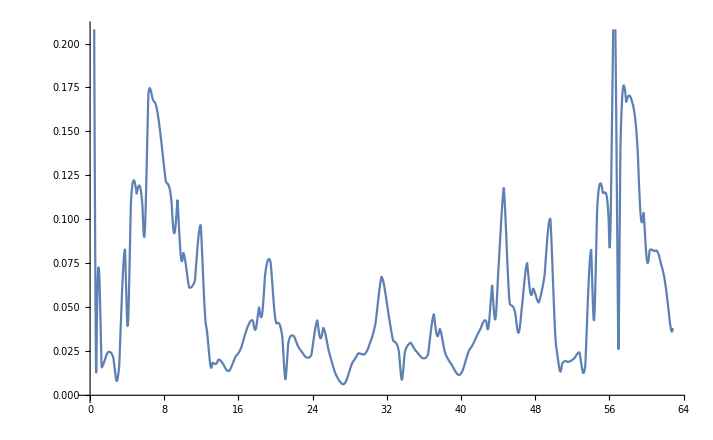

```mathematica
Plot[Abs[interpol21m1[t]],{t,ti,tf}]
```

```mathematica
neq=3;
a=Flatten[Table[{n1,l1,n2,l2,l},{n1, 2, neq},{l1, 1, n1-1},{n2, 2, neq},{l2, 1, n2-1}, {l,Abs[l1-l2],Abs[l1+l2]}],4];
b=Flatten[Table[{3,0,n2,l2,l},{n2, 2, neq},{l2, 1, n2-1}, {l,Abs[-l2],Abs[l2]}],2];
c=Flatten[Table[{n2,l2,3,0,l},{n2, 2, neq},{l2, 1, n2-1}, {l,Abs[-l2],Abs[l2]}],2];
d={{3,0,3,0,0}};
Join[a,b,c,d]
```

{{2,1,2,1,0},{2,1,2,1,1},{2,1,2,1,2},{2,1,3,1,0},{2,1,3,1,1},{2,1,3,1,2},{2,1,3,2,1},{2,1,3,2,2},{2,1,3,2,3},{3,1,2,1,0},{3,1,2,1,1},{3,1,2,1,2},{3,1,3,1,0},{3,1,3,1,1},{3,1,3,1,2},{3,1,3,2,1},{3,1,3,2,2},{3,1,3,2,3},{3,2,2,1,1},{3,2,2,1,2},{3,2,2,1,3},{3,2,3,1,1},{3,2,3,1,2},{3,2,3,1,3},{3,2,3,2,0},{3,2,3,2,1},{3,2,3,2,2},{3,2,3,2,3},{3,2,3,2,4},{3,0,2,1,1},{3,0,3,1,1},{3,0,3,2,2},{2,1,3,0,1},{3,1,3,0,1},{3,2,3,0,2},{3,0,3,0,0}}

```mathematica
FullSimplify[(4 c^4 h^4 (-4 c^2 h^2+3 a0^2 asum^2 q^2) (-4 c^2 h^2+27 a0^2 asum^2 q^2) (16 c^4 h^4-216 a0^2 asum^2 c^2 h^2 q^2+243 a0^4 asum^4 q^4))/(4 c^2 h^2+9 a0^2 asum^2 q^2)^6]
```

```mathematica
(4 c^4 h^4 (4 c^2 h^2-27 a0^2 asum[t]^2 q^2) (4 c^2 h^2-3 a0^2 asum[t]^2 q^2) (16 c^4 h^4-216 a0^2 asum[t]^2 c^2 h^2 q^2+243 a0^4 asum[t]^4 q^4))/(4 c^2 h^2+9 a0^2 asum[t]^2 q^2)^6
```

```mathematica
ListInterpolation[]
```